```mathematica
Clear["Global`*"]
```

```mathematica
μ = 3.8284
listcircle = {}
For[R = 0, R<1.0,R+0.1;
For[θ=0, θ<2 Pi, θ+0.1;
x = R Sin[θ] + 0.5;
y = R Cos[θ];
AppendTo[listcircle, {x,y}]]]
```

3.8284

{}

$Aborted

```mathematica
liss = {}
For[θ=0, θ<2 π, θ+π;
x = 1 Sin[θ] + 0.5;
y = 1 Cos[θ];
AppendTo[liss,{x,y}]]
```

{}

$Aborted

π

```mathematica
Sin[2π/3]
```

(√3)/2

```mathematica
μ = 3.8284;
listx = Range[0,0.5,0.001];
listy = Range[0,0.1,0.001];
colourplotsh ={};
For[i=0,i<Length[listy],i++;
localcolourpoints = {};
y = listy⟦i⟧;
For[j=0,j<Length[listx],j++;
x = listx⟦j⟧;
AppendTo[localcolourpoints,{x,y}]];
AppendTo[colourplotsh,localcolourpoints]]
```

```mathematica
colourplotsh1={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ-x^2 μ+y^2 μ;
yn[x_,y_] = y μ-2 x y μ;
For[m=0,m<Length[colourplotsh],m++;
localcolourpoints1 = {};
For[n=0,n<Length[colourplotsh⟦m⟧],n++;
xlocal = colourplotsh⟦m,n,1⟧;
ylocal = colourplotsh⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints1,{x1,y1}]];
AppendTo[colourplotsh1,localcolourpoints1]]
```

```mathematica
colourplotsh2={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] =x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
yn[x_,y_] = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
For[m=0,m<Length[colourplotsh],m++;
localcolourpoints2 = {};
For[n=0,n<Length[colourplotsh⟦m⟧],n++;
xlocal = colourplotsh⟦m,n,1⟧;
ylocal = colourplotsh⟦m,n,2⟧;
{x2 ,y2}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints2,{x2,y2}]];
AppendTo[colourplotsh2,localcolourpoints2]]
```

```mathematica
colourplotsh3={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
yn[x_,y_] = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
For[m=0,m<Length[colourplotsh],m++;
localcolourpoints3 = {};
For[n=0,n<Length[colourplotsh⟦m⟧],n++;
xlocal = colourplotsh⟦m,n,1⟧;
ylocal = colourplotsh⟦m,n,2⟧;
{x3 ,y3}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints3,{x3,y3}]];
AppendTo[colourplotsh3,localcolourpoints3]]
```

```mathematica
listploth1={};
For[i=0,i<Length[listy],i++;
ploth=ListPlot[colourplotsh1⟦i⟧,PlotStyle->Hue[i/(1.15Length[listy])]];
AppendTo[listploth1,ploth]];
```

```mathematica
listploth2={};
For[i=0,i<Length[listy],i++;
ploth=ListPlot[colourplotsh2⟦i⟧,PlotStyle->Hue[i/(1.15Length[listy])]];
AppendTo[listploth2,ploth]];
```

```mathematica
listploth3={};
For[i=0,i<Length[listy],i++;
ploth=ListPlot[colourplotsh3⟦i⟧,PlotStyle->Hue[i/(1.15Length[listy])]];
AppendTo[listploth3,ploth]];
```

```mathematica
listploth={};
For[i=0,i<Length[listy],i++;
ploth=ListPlot[colourplotsh⟦i⟧,PlotStyle->Hue[i/(1.15Length[listy])]];
AppendTo[listploth,ploth]];
```

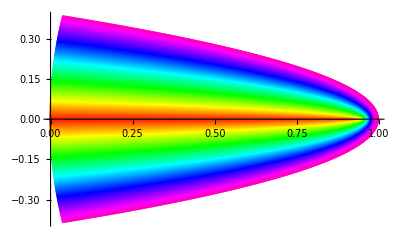

```mathematica
Show[listploth1, PlotRange-> All]
```

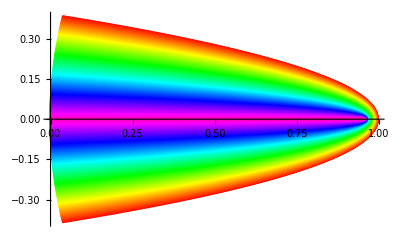

```mathematica
Show[listploth1, PlotRange-> All]
```

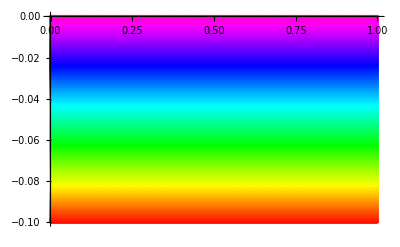

```mathematica
Show[listploth, PlotRange-> All]
```

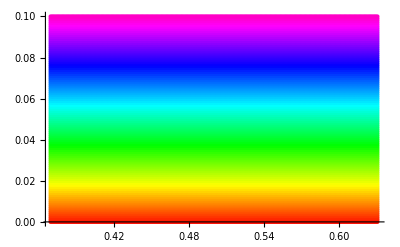

```mathematica
Show[listploth, PlotRange-> All]
```

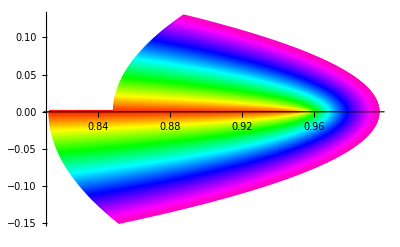

```mathematica
Show[listploth1, PlotRange-> All]
```

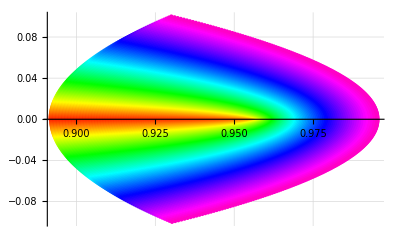

```mathematica
Show[listploth1, PlotRange-> All, GridLines-> Automatic]
```

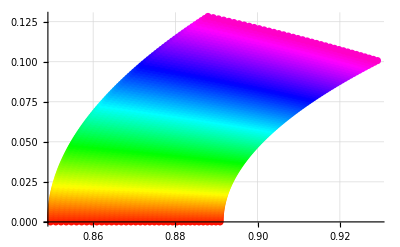

```mathematica
Show[listploth1, PlotRange-> All, GridLines-> Automatic]
```

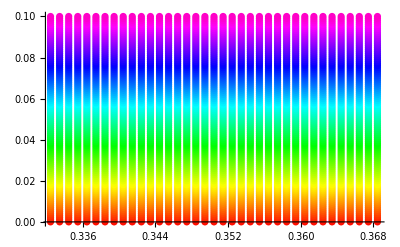

```mathematica
Show[listploth, PlotRange-> All]
```

## Horizontal

## y > 0

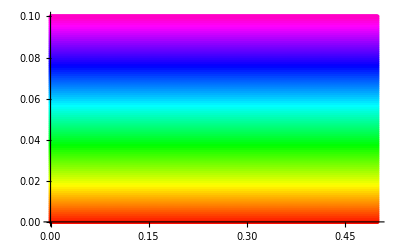

```mathematica
a= Show[listploth, PlotRange-> All]
```

x between 0 and 0.5

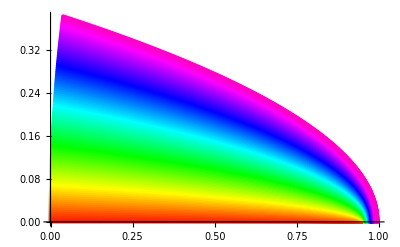

```mathematica
Show[listploth1, PlotRange-> All]
```

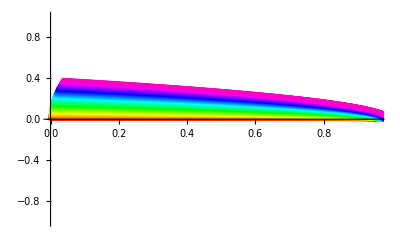

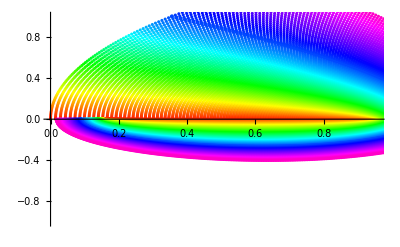

```mathematica
Show[listploth2]
```

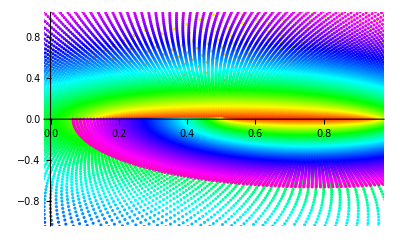

```mathematica
Show[listploth3]
```

x between 0.5 and 1.0

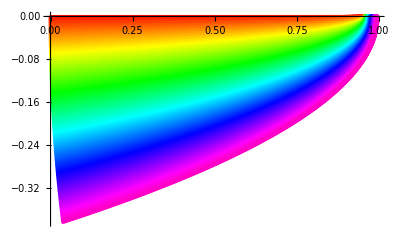

```mathematica
Show[listploth1,PlotRange-> All]
```

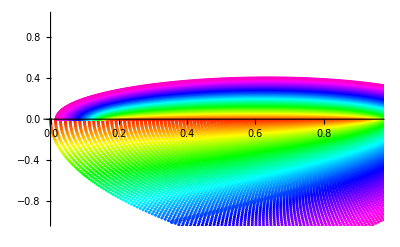

```mathematica
Show[listploth2]
```

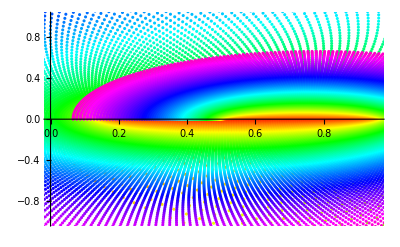

```mathematica
Show[listploth3]
```

## y < 0

x between 0 and 0.5

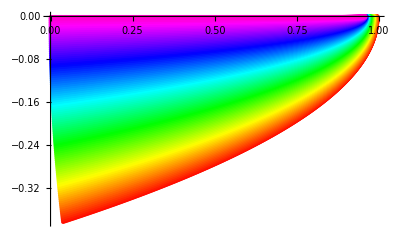

```mathematica
Show[listploth1]
```

```mathematica
Show[listploth2]
```

-Graphics-

```mathematica
Show[listploth3]
```

-Graphics-

x between 0.5 and 1.0

```mathematica
Show[listploth1]
```

-Graphics-

```mathematica
Show[listploth2]
```

-Graphics-

```mathematica
Show[listploth3]
```

-Graphics-

```mathematica
listx = Range[0,0.5,0.001];
listy = Range[0,0.1,0.001];
colourplotsv ={};
For[i=0,i<Length[listx],i++;
localcolourpoints = {};
x= listx⟦i⟧;
For[j=0,j<Length[listy],j++;
y = listy⟦j⟧;
AppendTo[localcolourpoints,{x,y}]];
AppendTo[colourplotsv,localcolourpoints]]
```

```mathematica
colourplotsv1={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ-x^2 μ+y^2 μ;
yn[x_,y_] = y μ-2 x y μ;
For[m=0,m<Length[colourplotsv],m++;
localcolourpoints1 = {};
For[n=0,n<Length[colourplotsv⟦m⟧],n++;
xlocal = colourplotsv⟦m,n,1⟧;
ylocal = colourplotsv⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints1,{x1,y1}]];
AppendTo[colourplotsv1,localcolourpoints1]]
```

```mathematica
colourplotsv2={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
yn[x_,y_] =y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
For[m=0,m<Length[colourplotsv],m++;
localcolourpoints2 = {};
For[n=0,n<Length[colourplotsv⟦m⟧],n++;
xlocal = colourplotsv⟦m,n,1⟧;
ylocal = colourplotsv⟦m,n,2⟧;
{x2 ,y2}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints2,{x2,y2}]];
AppendTo[colourplotsv2,localcolourpoints2]]
```

```mathematica
colourplotsv3={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
yn[x_,y_] = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
For[m=0,m<Length[colourplotsv],m++;
localcolourpoints3 = {};
For[n=0,n<Length[colourplotsv⟦m⟧],n++;
xlocal = colourplotsv⟦m,n,1⟧;
ylocal = colourplotsv⟦m,n,2⟧;
{x3 ,y3}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[localcolourpoints3,{x3,y3}]];
AppendTo[colourplotsv3,localcolourpoints3]]
```

```mathematica
listplotv={};
For[i=0,i<Length[listx],i++;
plotv=ListPlot[colourplotsv⟦i⟧,PlotStyle->Hue[i/(1.15Length[listx])]];
AppendTo[listplotv,plotv]];
```

```mathematica
listplotv1={};
For[i=0,i<Length[listx],i++;
plotv=ListPlot[colourplotsv1⟦i⟧,PlotStyle->Hue[i/(1.15Length[listx])]];
AppendTo[listplotv1,plotv]];
```

```mathematica
listplotv2={};
For[i=0,i<Length[listx],i++;
plotv=ListPlot[colourplotsv2⟦i⟧,PlotStyle->Hue[i/(1.15Length[listx])]];
AppendTo[listplotv2,plotv]];
```

```mathematica
listplotv3={};
For[i=0,i<Length[listx],i++;
plotv=ListPlot[colourplotsv3⟦i⟧,PlotStyle->Hue[i/(1.15Length[listx])]];
AppendTo[listplotv3,plotv]];
```

```mathematica
Show[listplotv, PlotRange-> Automatic]
```

-Graphics-

```mathematica
Show[listplotv1, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv]
```

-Graphics-

```mathematica
Show[listplotv1, PlotRange-> All]
```

-Graphics-

## Vertical

## y > 0

x between 0 and 0.5

```mathematica
Show[listplotv1, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv2, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv3, PlotRange-> {{0,1},Automatic}]
```

-Graphics-

x between 0.5 and 1.0

```mathematica
Show[listplotv1, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv2, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv3, PlotRange-> All]
```

-Graphics-

## y < 0

x between 0 and 0.5

```mathematica
Show[listplotv1, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv2, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv3, PlotRange-> All]
```

-Graphics-

x between 0.5 and 1.0

```mathematica
Show[listplotv1, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv2, PlotRange-> All]
```

-Graphics-

```mathematica
Show[listplotv3, PlotRange-> All]
```

-Graphics-